## Section | Phase Space Representations

This chapter introduces the use of characteristic functions and phase-space quasi-probability distributions in quantum optics. It outlines how characteristic functions provide a unified framework for generating different quasi-probability distributions, including the Wigner, Husimi–Q, and Glauber–Sudarshan P functions for representing quantum states. In depth discussion is dedicated to the Wigner and Husimi-Q functions, stating their properties and examples. The discussion extends to two-mode Wigner distributions, highlighting their application to entangled field states.

### Key Concepts

Relation between classical and quantum worlds via phase space

Quasi-probability distributions

Phase space visualization of quantum states

Non-classical signatures of quantum states

### Optical phase space

In quantum optics, the optical phase space provides a framework for representing the states of a single mode (or multiple modes) of the quantized electromagnetic field in terms of variables analogous to the position and momentum of a classical harmonic oscillator. For a single mode with annihilation and creation operators a and a^†, the quadrature operators shown in Chapter 1 are directly related to position and momentum(possibly up to a scaling factor).

Get the quadrature operators:

```mathematica
quadOps= QuadratureOperators[];
```

A Fock state has zero expectation of both quadratures, this fact can also be derived from the wave functions of the quantum harmonic oscillator:

```mathematica
With[{state = FockState[RandomInteger[{0,$FockSize-1}]]},(SuperDagger[state]@#@state)["Scalar"]& /@quadOps]
```

{0,0}

But it still has non zero variance ((2n+1)/4) in dimensionless scale:

```mathematica
OperatorVariance[FockState[4],#]&/@quadOps
```

{9/4,9/4}

The displacement operator plays the role of phase space translation. In the same way it can displace the vacuum to generate coherent states, it can be applied to other states modifying the expectation of quadratures

Coherent state quadrature expectations:

```mathematica
αc = 0.5 +0.6 ⅈ;
ψ = CoherentState[][αc];
means =Chop[(SuperDagger[ψ]@#@ψ)["Scalar"]&/@ QuadratureOperators[]];
```

Check they are equal to Re(α) and Im(α):

```mathematica
means==ReIm[αc]
```

True

Displaced Fock state quadrature expectations, also relate to Re(α) and Im(α) of the displacement

Apply D(α) to the state |2⟩:

```mathematica
ψdisp =DisplacementOperator[0.2+0.5ⅈ][FockState[2]];
```

Calculate the variances:

```mathematica
Chop[(SuperDagger[ψdisp]@#@ψdisp)["Scalar"]&/@ QuadratureOperators[]]
```

{0.2,0.5}

An intuitive representation is to denote the Fock states in phase space as concentric circles centered at the origin since average value is zero and variance non zero(equal in both quadratures)

```mathematica
Module[{colors,disks},colors=Table[RandomColor[],{10}];
disks=Table[{Directive[colors[[n+1]],Opacity[0.4]],Disk[{0,0},(2 n+1)/4]},{n,5,0,-1}];
Legended[Graphics[disks,Axes->True,AxesOrigin->{0,0},PlotRange->{{-5,5},{-5,5}},ImageSize->300],SwatchLegend[colors,Table["Fock state "<>ToString[n],{n,0,5}],LegendLayout->"Column"]]]
```

-Graphics-

We will see there is a more interesting approach to represent quantum states, specifying a function of x and p that can encode all the relevant information about the state. These functions are mathematical artifacts that allow extracting the distribution of position and momentum, they are not the standard joint distribution of x and p otherwise it would violate Heisenberg principle! We will reach to that in the next sections

### Generators: Characteristic Functions

If we have a probability density p(x) associated with a random variable X, it should be the case that p(x) >= 0   ∀ x ∈ ℝ and ∫ p(x) ⅆx=1 . The nth moment of the probability density is  ⟨x^n⟩ = ∫x^n p(x)ⅆx,  the function p(x)  can be determined if information of  all the moments is known.

We can define a characteristic function

C(k)= ⟨ⅇ^(ⅈ k x) ⟩ = ∫ ⅇ^(ⅈ k x) p(x)ⅆx = (∑^)_(n=0)^∞(ⅈ k)^n/(n!)⟨x^n⟩

so they are related by a Fourier transform p(x)=1/(2 π)∫ ⅇ^(-ⅈ k x)C(k) ⅆk

As an example, let’s take the Gaussian distribution as p(x)

```mathematica
dist=NormalDistribution[μ,σ];
PDF[dist,x]
```

(ⅇ^(-(x-μ)^2/(2 σ^2)))/(√(2 π) σ)

We can use CharacteristicFunction to calculate C(k):

```mathematica
cf=CharacteristicFunction[dist,k]
```

ⅇ^(ⅈ k μ-(k^2 σ^2)/2)

A Gaussian in x has been transformed to a Gaussian in k, the Gaussian can be said to be a fixed point for this Fourier kernel. Notice the reciprocity of the two widths, σ sits in the denominator of the exponent for p(x) and in the numerator for C(k)

For comparison of the moments, we can read them off directly from expansion of C(k), or computing them from the definition using p(x):

```mathematica
fromCFmoments=Table[(-ⅈ)^n n! SeriesCoefficient[cf,{k,0,n}],{n,0,5}]
```

{1,μ,μ^2+σ^2,μ^3+3 μ σ^2,μ^4+6 μ^2 σ^2+3 σ^4,μ^5+10 μ^3 σ^2+15 μ σ^4}

```mathematica
pxmoments =Expand@Table[Moment[dist,n],{n,0,5}]
```

{1,μ,μ^2+σ^2,μ^3+3 μ σ^2,μ^4+6 μ^2 σ^2+3 σ^4,μ^5+10 μ^3 σ^2+15 μ σ^4}

Computing the inverse Fourier transform to recover p(x) from C(k):

```mathematica
Simplify[InverseFourierTransform[cf,k,x,FourierParameters->{1,1}],σ>0]==PDF[dist,x]
```

True

Three characteristic functions are important in quantum optics:

C_W(λ)= Tr[ ρ̂ ⅇ^(λ (â)^†-λ*â)] = Tr[ ρ̂ D̂(λ)]   (Wigner)

C_N(λ)= Tr[ ρ̂ ⅇ^(λ (â)^†)ⅇ^(-λ*â)]           (normally ordered)

C_A(λ)= Tr[ ρ̂ ⅇ^(-λ (â)^†)ⅇ^(λ*â)]   (antinormally ordered)

related by  C_W(λ) = C_N(λ)ⅇ^(-1/2 |λ|^2)=C_A(λ)ⅇ^(1/2 |λ|^2)
There is also a general parametrized characteristic function with parameter s:

C(λ,s)= Tr[ ρ̂ exp(λ (â)^†-λ*â+s|λ|^2/2)]

such that C(λ,0) = C_W(λ),  C(λ,1) = C_N(λ) and C(λ, -1) = C_A(λ)

#### Relation between characteristic functions and quasi-probability distributions

The characteristic functions are related to quasi-probability distributions , they are linked via the Fourier transform. Those quasi-probability distributions are the mathematical objects that we will use to describe quantum states in phase space

Wigner:

W(α)=1/π^2 ∫ exp(λ^*α-λ α*)C_W(λ)ⅆ^2 λ

Husimi-Q function:

Q(α)=1/π^2 ∫ exp(λ^*α-λ α*)C_A(λ)ⅆ^2 λ

Glauber-Sudarshan P-function:

P(α)=1/π^2 ∫ exp(λ^*α-λ α*)C_N(λ)ⅆ^2 λ

s-parameter quasi-probability function:

W_s(α)=1/π^2 ∫ exp(λ^*α-λ α*)C(λ,s)ⅆ^2 λ

The s-parameter quasi-probability function can generate the other ones picking certain values of s.

s = +1       ⟹  W_(+1)(α)=P(α)
s =    0        ⟹  W_0(α) = W(α)
s = -1       ⟹  W_-1(α) =Q(α)

Computationally these functions can be demanding to calculate for an arbitrary state or density matrix . There are good numerical techniques to compute the Wigner and Husimi Q-function , but not for the Glauber P-because it is highly singular in general.

The Husimi function is always positive, unlike the Wigner and P-function that can take negative values in some region that  indicate non-classical behavior, however the converse is not a true a state can be non-classical and still have positive Wigner function.

The P-function is a good theoretical tool but can be impractical in many cases, this is why the preferred of all three is the Wigner because it can also show quantum nature of non-classical states (unlike Husimi).

### Wigner function

In terms of wave functions the Wigner function can be calculated as:

W(x,p) = 1/(π ℏ)  ∫_(-∞)^∞ ψ*(x-y/2)ψ(x+y/2) ⅇ^(ⅈ p y/ℏ)ⅆy

Other way of calculating the Wigner function for a density operator ρ is:

W(α)=2/π Tr[ρ̂ D̂(α)ⅇ^(ⅈ π (â)^†â)(D̂)^†(α)]    with α=(x + ⅈ p)/(√2)

The Wigner function is normalized in phase space, this means the integral over all phase space is equal to 1 (this also holds for Husimi-Q and Glauber-Sudarshan):

∫ ∫ W(x,p)(x,p)ⅆx ⅆp =1

The Wigner function also has other important property, integrating over one of the variables (a marginal) reflects a probability density consistent with quantum measurement theory (this does not hold for Husimi-Q and Glauber-Sudarshan)

Position distribution:

∫ W(x,p)ⅆp = ⟨x|ρ̂|x⟩

Momentum distribution:

∫ W(x,p)ⅆx = ⟨p|ρ̂|p⟩

Operator expectation values are calculated as phase space averages of the Wigner function, say for an operator Â that is a function of the operators x̂ and p̂:

⟨Â⟩= Tr[ρ̂ Â] =∫_(-∞)^∞ ∫_(-∞)^∞ W(x,p) A_W(x,p)ⅆxⅆp

A_W is the Weyl symbol of the operator, trivial cases are A_W(x) =x and  A_W(p)=p (or when is a function of only x or p)

In the Quantum Framework, we can use WignerRepresentation:

Define the superposition state 1/(√2)( |0⟩ + |1⟩):

```mathematica
ψ = QuantumState["+",$FockSize]
```

1/(√2)0+1/(√2)1

Get the function that represents the phase space representation in the selected rectangular phase space domain:

```mathematica
wig = WignerRepresentation[ψ,{-4,4},{-4,4}]
```

InterpolatingFunction[…]

Plot the function:

```mathematica
Plot3D[wig[x,p],{x,-4,4},{p,-4,4},]
```

-Graphics-

Normalization condition:

```mathematica
Integrate[wig[x,p],{x,-4,4},{p,-4,4}]
```

0.999999

Integrating along one of the variables to get marginals:

```mathematica
posMarginal =Integrate[wig[x,p],{p,-4,4}];
momenMarginal =Integrate[wig[x,p],{x,-4,4}];
```

Position marginal:

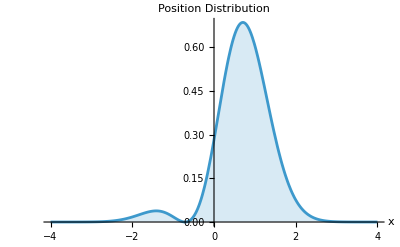

```mathematica
Plot[posMarginal,{x,-4,4},Filling->Bottom,AxesLabel->{"x", "Position Distribution"}]
```

Momentum marginal:

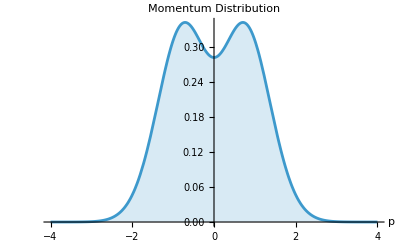

```mathematica
Plot[momenMarginal,{p,-4,4},Filling->Bottom,AxesLabel->{"p", "Momentum Distribution"}]
```

Average position:

```mathematica
NIntegrate[x posMarginal,{x,-4,4}]
```

0.707106

Average momentum:

```mathematica
NIntegrate[p momenMarginal,{p,-4,4},Method->"LocalAdaptive"]//Chop
```

0

Explicit calculation of the expectations values using quadrature operators:

```mathematica
(SuperDagger[ψ]@(√2#)@ψ)["Scalar"]& /@QuadratureOperators[]
```

{1/(√2),0}

The trace definition can be rewritten in terms of a kernel 𝒦 as W(α)=2/π Tr[ρ̂· 𝒦(α)]

And the associated matrix elements of the kernel in the Fock space are

⟨m|𝒦_a(α)|n⟩ = (-1)^n ⅇ^(-|ζ|^2/2) Piecewise[{{√((n!)/(m!))ζ^(m-n)(L_n^(m-n)(|ζ|))^2, m≥n}, {√((m!)/(n!)) (-ζ*)^(n-m) L_m^(m-n)(|ζ|^2), n≥m}}]

where L_m^n are Laguerre generalized polynomials

This calculation is done by WignerFunction, calling it for the superposition state:

```mathematica
func =WignerFunction[ψ,{x,p}]
```

Plot the function, of course we get the same result as before:

```mathematica
Plot3D[func,{x,-4,4},{p,-4,4},]
```

-Graphics-

Integral over all phase space, the returned function already included a 1/2 factor due to how the differentials of α and x and p relate (α = (x + ⅈ p)/√2):

```mathematica
∫_(-∞)^∞ ∫_(-∞)^∞ funcⅆpⅆx
```

1

Symbolic marginal of x:

```mathematica
xmarginal=∫_(-∞)^∞ funcⅆp
```

(ⅇ^(-x^2) (2 x (x+√2)+1))/(2 √π)

Symbolic marginal of p:

```mathematica
pmarginal = Integrate[func,{x,-∞,∞}]
```

(ⅇ^(-p^2) (2 p^2+1))/(2 √π)

Plotting the marginals:

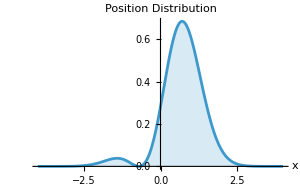

```mathematica
Plot[xmarginal,{x,-4,4},]
```

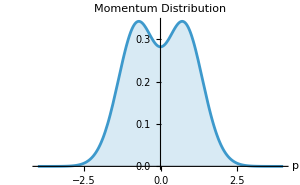

```mathematica
Plot[pmarginal,{p,-4,4},]
```

Let’s calculate the Wigner function for the Fock states |0⟩, |2⟩, |5⟩ and a coherent state |α⟩. Fock states |n⟩(n≥1) have negative values in their Wigner function showing they are non-classical. In phase space, the vacuum and any coherent state have a gaussian distribution ,the value of α indicates the displacement of the gaussian respect to the origin (up to some possible scaling factors)

Compute the Wigner representations:

```mathematica
wigners =WignerRepresentation[#,{-4,4},{-4,4}]&/@{FockState[0],FockState[2],FockState[5],CoherentState[][0.5+0.8ⅈ]};
```

Plot the functions:

```mathematica
plots=Plot3D[#[x,y],{x,-4,4},{y,-4,4},]&/@wigners;
```

Show the results:

```mathematica
Legended[Grid@Partition[plots,{2}],]
```

-Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D-

#### Additional examples and more properties of the Wigner Function

Cat state usage in the QuantumFramework, more about cat states in future chapters. In simple terms is a superposition of coherent states:

```mathematica
ψ =CatState[40][2.8,π];
```

Compute the Wigner function:

```mathematica
wigFunc = WignerRepresentation[ψ,{-8,8},{-8,8}];
```

3D plot:

```mathematica
plotThree =Plot3D[wigFunc[x,y],{x,-6,6},{y,-6,6},];
```

Density plot projection:

```mathematica
proj =SliceDensityPlot3D[wigFunc[x,p],z==-0.35,{x,-6,6},{p,-6,6},{z,-0.4,-0.3},];
```

Show the combined plot:

```mathematica
Show[plotThree,proj,BoxRatios->{2, 2, 1},ImageSize->400]
```

-Graphics-

Getting the marginals:

```mathematica
{xMarg,pMarg}=Table[Integrate[wigFunc[x,p],{i,-6,6}],{i,{p,x}}];
```

Plot the marginals:

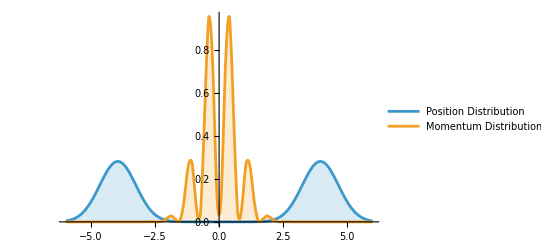

```mathematica
Plot[{xMarg,pMarg/.p->x},{x,-6,6},]
```

Compass state, superposition of coherent states in the vertices of a regular phase space polygon:

```mathematica
compassState[n_,α_] :=Sum[CoherentState[][α Exp[(ⅈ 2π k)/n]],{k,1,n}]["Normalize"];
```

Increase truncation size:

```mathematica
SetFockSpaceSize[40];
```

Wigner function of an hexagonal compass state:

```mathematica
wig =WignerFunction[compassState[6,3.1],(x+ⅈ p)/(√2)];
```

Plot the function:

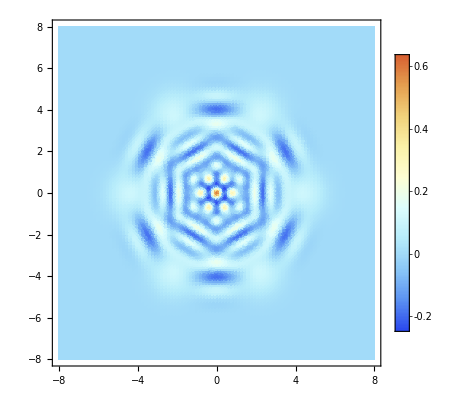

```mathematica
DensityPlot[Re@wig,{x,-8,8},{p,-8,8},]
```

Transpose operation T of density operator ρ does a mirror reflection in phase space to the Wigner function:

ρ̂→ (ρ̂)^T  ⟺ W(q,p)→ W(q,-p)

Superposition of Fock states with a relative phase as a matrix state:

```mathematica
ρ =( 1/(√2)(FockState[0]+ⅈ FockState[1]))["MatrixState"];
```

Wigner function:

```mathematica
WignerFunction[ρ,α]
```

(2 (-ⅈ α ⅇ^(-2 Abs[α]^2)+1/2 ⅇ^(-2 Abs[α]^2)-1/2 ⅇ^(-2 Abs[α]^2) (1-4 Abs[α]^2)+ⅈ ⅇ^(-2 Abs[α]^2) Conjugate[α]))/π

Check equality, since α=(x+ⅈ p)/(√2) changing p to -p is equivalent to changing α to α*, and for Hermitian density matrices ρ^T=ρ*:

```mathematica
FullSimplify[WignerFunction[ψ,α]-WignerFunction[ψ["Conjugate"],α*]]
```

0

Symplectic covariance property W_(U ρ U^†)(ξ)=W_ρ(S ξ),  means that the Wigner function of a state transformed in Hilbert space can be obtained from the Wigner function of the original state — by applying the corresponding linear symplectic transformation to the phase-space coordinates.

Let’s try  as an example for phase space rotations:

```mathematica
SetFockSpaceSize[];
```

Random pure state:

```mathematica
ρ = QuantumState["RandomPure",$FockSize];
```

Rotating the state in Hilbert space:

```mathematica
shiftedwig =WignerFunction[PhaseShiftOperator[θ]@ρ,α];
```

Rotating the phase space coordinate, using x and p would be rotation matrix for complex α we can just use ⅇ^(-ⅈ θ):

```mathematica
func =WignerFunction[ρ,α ⅇ^(-ⅈ θ)];
```

Equality:

```mathematica
Chop[Simplify[shiftedwig-func,θ∈Reals]]
```

0

### Husimi-Q function

A simpler definition for calculating the Husimi-Q function is (first equality only valid for pure states):

Q(α)=1/π|⟨α| ψ⟩|^2 = 1/π⟨α|ρ̂|α⟩

This idea is implemented for symbolic outputs in HusimiQFunction

Fock state |4⟩:

```mathematica
ψ = FockState[4];
```

Compute the function in the phase space variables:

```mathematica
husimipure = HusimiQFunction[ψ,{x,p}]
```

1/2 ((x^8 ⅇ^(-p^2-x^2) √(ⅇ^(p^2+x^2)))/(384 π)+(p^2 x^6 ⅇ^(-p^2-x^2) √(ⅇ^(p^2+x^2)))/(96 π)+(p^8 ⅇ^(-p^2-x^2) √(ⅇ^(p^2+x^2)))/(384 π)+(p^6 x^2 ⅇ^(-p^2-x^2) √(ⅇ^(p^2+x^2)))/(96 π)+(p^4 x^4 ⅇ^(-p^2-x^2) √(ⅇ^(p^2+x^2)))/(64 π))

Visualize the Husimi-Q function of the state |4⟩:

```mathematica
Plot3D[husimipure,{x,-4,4},{p,-4,4},]
```

-Graphics3D-

We see the Husimi-Q function has values greater than zero. For Fock states |n⟩ it has symmetric ring shape, and the radius of the ring increases when n increases

Normalization of the function:

```mathematica
∫_(-∞)^∞ ∫_(-∞)^∞ husimipureⅆpⅆx
```

1

Position marginal:

```mathematica
xMarginal =Integrate[husimipure,{p,-∞,∞}]
```

(ⅇ^(-x^2/2) (x^8+4 x^6+18 x^4+60 x^2+105))/(384 √(2 π))

Plot the marginal:

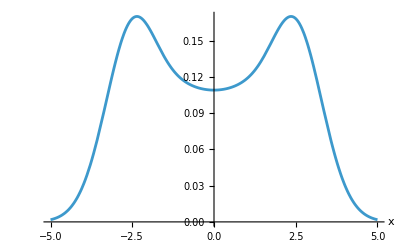

```mathematica
Plot[xMarginal,{x,-5,5},]
```

Attempting to compute ⟨ x^2 ⟩:

```mathematica
Integrate[x^2 xMarginal,{x,-∞,∞}]
```

5

We see is not correct and it differs from the exact value, only Wigner gives correct marginals to compute average values:

```mathematica
(SuperDagger[ψ]@((√2 QuadratureOperators[][[1]])^2)@ψ)["Scalar"]
```

9/2

The Husimi-Q function of a coherent state is also a gaussian function, also for any state 0< Q(α)<=1/π and that upper bound is attained for coherent states. In terms of x and p coordinates the maximum is 1/(2 π) because of extra factor to make it normalized

Let’s try with a coherent state with α = 0.5 + 0.5 ⅈ:

```mathematica
ψ = CoherentState[][0.5+0.5ⅈ];
```

Get the symbolic function:

```mathematica
husimipure=Chop@HusimiQFunction[ψ,{x,p}];
```

Visualize the function, we see it has a Gaussian shape:

```mathematica
Plot3D[husimipure,{x,-4,4},{p,-4,4},]
```

-Graphics-

Upper bound numerical verification:

```mathematica
Chop[NMaximize[husimipure,{x,p}][[1]]-1/(2π)]
```

0

Husimi-Q function of a superposition of Fock states presents interesting geometric symmetrical shapes. The patterns depend on the difference of number states values:

“Number hopping” state (try changing the number 5 to something else):

```mathematica
ψ = Sum[FockState[i],{i,2,$FockSize,5}]["Normalize"]
```

1/(√3)2+1/(√3)7+1/(√3)12

We follow the same method:

```mathematica
husimipure = HusimiQFunction[ψ,(x+ⅈ p)/(√2)];
```

Visualize the density plot:

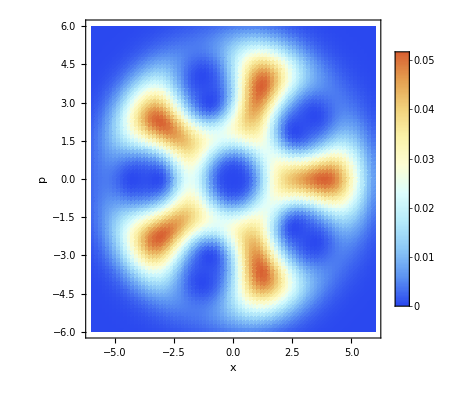

```mathematica
DensityPlot[Re@husimipure,{x,-6,6},{p,-6,6},]
```

This definition looks apparently perfect for computational exploration, however, when the truncation size is bigger or the density matrix is heavily occupied performance issues can start to appear. In the QuantumFramework we have HusimiQRepresentation  which is adequate for any state

Set the truncation size to 50:

```mathematica
SetFockSpaceSize[50];
```

Define a statistical mixture of coherent states:

```mathematica
ψ = 2/3 CoherentState[][2.5]["Operator"]+1/3 CoherentState[][-2.5]["Operator"];
```

Implement the Husimi-Q definition for mixed states:

```mathematica
husimimixed =With[{s=CoherentState["Normalized"->False]},1/π Exp[-Abs[α]^2](SuperDagger[s[α]]@ψ@s[α])["Scalar"]/. α->(x+ⅈ p)/(√2)];
```

Plot the results:

```mathematica
Plot3D[1/2Re@husimimixed,{x,-8,8},{p,-8,8},]//AbsoluteTiming
```

-Graphics-

Same state as before but as a QuantumState:

```mathematica
ψ2 =2/3CoherentState[][2.5]["MatrixState"]+1/3CoherentState[][-2.5]["MatrixState"];
```

Compute the Husimi-Q function in a rectangular phase space region:

```mathematica
husi =HusimiQRepresentation[ψ2,{-8,8},{-8,8}];//EchoTiming
```

0.445674

Also use the symbolic function:

```mathematica
husi2 =HusimiQFunction[ψ2,(x+ⅈ p)/(√2)];//EchoTiming
```

0.263116

Plot the results:

```mathematica
Plot3D[husi[x,p],{x,-8,8},{p,-8,8},]//AbsoluteTiming
```

-Graphics-

```mathematica
Plot3D[Re@husi2,{x,-8,8},{p,-8,8},]//AbsoluteTiming
```

-Graphics-

We see HusimiQRepresentation is faster for this demanding example considering the time of computing the function and evaluating it at phase space points

### Connection between quasi-probability distributions

By gaussian filtering(smoothing) it is possible to go from the Wigner function to the Husimi-Q function

Q(x,p)=1/π∫ ∫ W(x',p') exp(-(x-x')^2-(p-p')^2)ⅆx'ⅆp'

```mathematica
SetFockSpaceSize[20];
```

Get the phase space representations for state |2⟩:

```mathematica
{wig,husi}=#[FockState[2],{-4,4},{-4,4}]&/@{WignerRepresentation,HusimiQRepresentation};
```

Numerical integration:

```mathematica
Q[xα_,pα_]:= 1/π NIntegrate[wig[x,p] ⅇ^(-(x-xα)^2)ⅇ^(-(p-pα)^2),{x,-4,4},{p,-4,4},Method->"LocalAdaptive"]
```

Sample random points in the region:

```mathematica
diff =Abs[husi[#1,#2]-Q[#1,#2]]& @@@RandomReal[{-4,4},{50,2}];
```

Plot the absolute error:

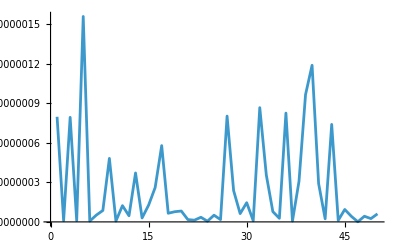

```mathematica
ListLinePlot[diff,PlotRange->All]
```

Symbolic Wigner function for state |3⟩ :

```mathematica
symbolicwig =WignerFunction[FockState[3],{x',p'}]
```

1/2 ((8 (p')^6 ⅇ^(-(p')^2-(x')^2))/(3 π)+(8 (p')^4 (x')^2 ⅇ^(-(p')^2-(x')^2))/π-(12 (p')^4 ⅇ^(-(p')^2-(x')^2))/π+(8 (p')^2 (x')^4 ⅇ^(-(p')^2-(x')^2))/π+(12 (p')^2 ⅇ^(-(p')^2-(x')^2))/π-(24 (p')^2 (x')^2 ⅇ^(-(p')^2-(x')^2))/π+(8 (x')^6 ⅇ^(-(p')^2-(x')^2))/(3 π)+(12 (x')^2 ⅇ^(-(p')^2-(x')^2))/π-(2 ⅇ^(-(p')^2-(x')^2))/π-(12 (x')^4 ⅇ^(-(p')^2-(x')^2))/π)

Performing the gaussian filtering integral:

```mathematica
gaussianSmoothed =1/π Integrate[symbolicwig ⅇ^(-(x'-x)^2-(p'-p)^2),{x',-∞,∞},{p',-∞,∞}]
```

(ⅇ^(-p^2/2-x^2/2) (p^2+x^2)^3)/(96 π)

We indeed recover the Husimi Q function of the state |3⟩:

```mathematica
FullSimplify[HusimiQFunction[FockState[3],{x,p}]-gaussianSmoothed,{x,p}∈Reals]
```

0

### S-parameter quasi-probability function and the P function limit

The s-parameter family of function can also be computed with a trace as W(α,s)=2/π Tr[ρ̂· 𝒦̂(α,s)]

And the associated matrix elements of the modified kernel in the Fock space are
⟨m|𝒦̂(α,s)|n⟩ = (ⅇ^(-|ζ|^2/[2(1-s)]))/(1- s) Piecewise[{{((s+1)/(s-1))^n √((n!)/(m!))(ζ/(1-s))^(m-n)(L_n^(m-n)((|ζ|)/(1-s^2)))^2, m≥n}, {((s+1)/(s-1))^m √((m!)/(n!))((ζ*)/(1-s))^(n-m) L_m^(n-m)((|ζ|^2)/(1-s^2)), n>m}}]

Consider the following Fock state:

```mathematica
ρ = FockState[4];
```

We can use SOrderedFunction to obtain a symbolic expression of the s-parametric quasi-probability function, which internally uses the trace definition:

```mathematica
sFunc =SOrderedFunction[ρ,{x,p},s]//FullSimplify
```

-1/(3 π (s-1)^9)ⅇ^((p^2+x^2)/(s-1)) (-3 (8 p^2+8 x^2-1)+2 (p^2+x^2)^2 (p^4+2 p^2 (x^2-4)+x^4-8 x^2+18)+3 s^8+12 s^6 (2 p^2+2 x^2-1)+18 s^4 (2 (p^4+2 p^2 (x^2-1)+x^4)-4 x^2+1)+4 s^2 (4 p^6+6 p^4 (2 x^2-3)+6 p^2 (2 x^4-6 x^2+3)+4 x^6-18 x^4+18 x^2-3))

We see is not possible to get a closed form P function just taking the s->1 limit, since it can involve derivatives of δ functions:

```mathematica
Limit[sFunc,s->1,Assumptions->{x,p}∈Reals]
```

Indeterminate

Generate plots increasing the s parameter:

```mathematica
plots = Table[Plot3D[Evaluate[sFunc/.s->s],{x,-4,4},{p,-4,4},],{s,0,0.9,0.1}]
```

Show the results:

```mathematica
GraphicsGrid@Partition[Rasterize[#,RasterSize->2500]&/@plots,{3}]
```

-Graphics-

Approaching the Glauber-Sudarshan P function limit s->1, we see the function gets progressively more singular according to the theory:

```mathematica
Plot3D[Evaluate[sFunc/.s->0.9],{x,-4,4},{p,-4,4},]
```

-Graphics-

It also has negative values(similar to Wigner), indication of non-classical behavior as expected for a Fock state:

```mathematica
NMinimize[Evaluate[sFunc/.s->0.9],{x,p}][[1]]
```

-118109.

### Joint Wigner Function

One way to define the joint Wigner function for two modes 𝑎, 𝑏 is through a trace expression that depends on the displacement and phase-shift (parity) operators.  Using the kernel 𝒦 that was defined before, it can be written as:

𝒲(α,β)=4/π^2 Tr[ρ̂(D̂)_a(α)ⅇ^(ⅈ π (â)^†a)((D̂)_a)^†(α)(D̂)_b(β)ⅇ^(ⅈ π (b̂)^†b)((D̂)_b)^†(β)]
= 4/π^2 Tr[ρ̂ 𝒦_a(α)𝒦_b(β)]

Some properties:

Normalization
 ∫∫ W(α,β)ⅆ^2 α ⅆ^2 β=1

For a separable state ρ = ρ_A ⊗ ρ_B, the joint Wigner function factorizes 
W_(A B)(x_A,x_B)=W_A(x_A)W_B(x_B)

Global inversion symmetry (always true): 
W(x_1,p_1,x_2,p_2)=W(-x_1,-p_1,-x_2,-p_2)

Partial transpose of the bipartite system does the following transformation to the Wigner function
PT: W(x_1,p_1,x_2,p_2)→ W(x_1,p_1,x_2,-p_2)

Parity symmetry (not general)
W(x_1,p_1,x_2,p_2)=W(-x_1,-p_1,x_2,p_2)

These functions now have four phase space coordinates (or two complex) so plotting them is not possible. A convenient way to reduce the dimension  is to plot slices fixing some coordinates, or to calculate marginals.

#### Implementation

Symbolic definition of 𝒦_mn:

```mathematica
Kmn[gamma_,m_,n_]:=With[{zeta=2 gamma},(-1)^n Exp[-(Abs[zeta]^2)/2] If[m>=n,Sqrt[n!/m!] If[m==n,1,Power[zeta,m-n]] LaguerreL[n,m-n,Abs[zeta]^2],Sqrt[m!/n!] Conjugate[-zeta]^(n-m) LaguerreL[m,n-m,Abs[zeta]^2]]]
```

Numeric compiled version of 𝒦_mn:

```mathematica
Kmncomp=FunctionCompile[Function[{Typed[γ,"ComplexReal64"],Typed[m,"Integer64"],Typed[n,"Integer64"]},Module[{ζ,res},ζ=2.0*γ;
res=If[m>=n,Sqrt[Gamma[n+1.0]/Gamma[m+1.0]]*If[m==n,1.+0.ⅈ,ζ^(m-n)]*LaguerreL[n,m-n,Abs[ζ]^2],Sqrt[Gamma[m+1.0]/Gamma[n+1.0]]*Conjugate[-ζ]^(n-m)*LaguerreL[m,n-m,Abs[ζ]^2]];
(-1)^n*Exp[-Abs[ζ]^2/2.0]*res]]]
```

CompiledCodeFunction[…]

Trace implementations (gain will depend on how sparse the density matrix is):

```mathematica
ClearAll[NWigner2mod]
NWigner2mod[rho_SparseArray,α_,β_]:=
With[
{d=√First[rho["Dimensions"]],vals=rho["ExplicitValues"],pos=rho["ExplicitPositions"]},
(4./π^2) Dot[vals,Kmncomp[α,Quotient[#2-1,d],Quotient[#1-1,d]]
			Kmncomp[β,Mod[#2-1,d],Mod[#1-1,d]]
				&@@@pos]]
```

```mathematica
ClearAll[Wigner2mod]
Wigner2mod[rho_SparseArray,α_,β_]:=
With[
{d=√First[rho["Dimensions"]],vals=rho["ExplicitValues"],pos=rho["ExplicitPositions"]},
(4/π^2) Dot[vals,Kmn[α,Quotient[#2-1,d],Quotient[#1-1,d]]
			Kmn[β,Mod[#2-1,d],Mod[#1-1,d]]
				&@@@pos]]
```

Let’s explore the two mode Wigner function of a NOON state, that is a superposition of two mode Fock states

```mathematica
SetFockSpaceSize[10];
```

FockState also supports multimode states:

```mathematica
FockState[{3,6}]
```

36

NOON state with N = 4, 1/(√2)(|0,4⟩ + |4,0⟩):

```mathematica
ψ =1/(√2)( FockState[{0,4}]+FockState[{4,0}]);
```

Joint Wigner function:

```mathematica
Wfunc = Function[{x1,p1,x2,p2},Simplify[Wigner2mod[ψ["DensityMatrix"],(x1+ⅈ p1)/(√2),(x2+ⅈ p2)/(√2)],Element[{x1,p1,x2,p2},Reals]]];
```

Check global symmetry:

```mathematica
Wfunc[x1,p1,x2,p2]-Wfunc[-x1,-p1,-x2,-p2]
```

0

Parity symmetry for NOON states only work when N is even:

```mathematica
Simplify[Wfunc[x1,p1,x2,p2]-Wfunc[-x1,-p1,x2,p2]]
```

0

3D slices (p_2=0):

```mathematica
func = Wigner2mod[ψ["DensityMatrix"],α,β]/.{α->(x1+ⅈ p1)/(√2),β->x2/(√2)};
```

Plot the slice:

```mathematica
DensityPlot3D[Re@func,{x1,-3,3},{p1,-3,3},{x2,-3,3},]
```

-Graphics-

Higher resolution plot:

#### Examples

We will explore more examples of the joint Wigner function for other two mode states, and verify some of the mathematical properties the functions have

Two mode Fock states

Set truncation size:

```mathematica
SetFockSpaceSize[8];
```

Density matrices for states |m,0⟩:

```mathematica
ρs=Array[FockState[{#,0}]["DensityMatrix"]&,6];
```

Spatial range :

```mathematica
range = N@Subdivide[-2,2,21];
```

Sample points for 3D slices(p_2=0):

```mathematica
sampsFock=Table[Flatten[Table[{x1,p1,x2,NWigner2mod[ρs[[i]],(x1+ⅈ p1)/(√2),x2/(√2)]},{x1,range},{p1,range},{x2,range}],2],{i,6}];
```

Resulting plots:

```mathematica
Grid@Partition[Table[ListDensityPlot3D[sampsFock[[n]],],{n,6}],2]
```

-Graphics-

```mathematica
ψ = FockState[{2,3}];
```

Check symmetry properties for state |2,3⟩:

```mathematica
wig = Function[{x1,p1,x2,p2},Evaluate@Simplify[Wigner2mod[ψ["DensityMatrix"],(x1+ⅈ p1)/(√2),(x2+ⅈ p2)/(√2)],Element[{x1,p1,x2,p2},Reals]]];
```

It is global and parity symmetric:

```mathematica
Simplify[wig[x1,p1,x2,p2]-wig[-x1,-p1,-x2,-p2]]
```

0

```mathematica
Simplify[wig[x1,p1,x2,p2]-wig[-x1,-p1,x2,p2]]
```

0

Check PT transformation:

```mathematica
Wigner2mod[QuantumPartialTranspose[ψ,{2}]["DensityMatrix"],α,Conjugate[β]]-Wigner2mod[ψ["DensityMatrix"],α,β]//Simplify
```

0

Check separability:

```mathematica
Wigner2mod[ψ["DensityMatrix"],α,β]-WignerFunction[FockState[2],α]WignerFunction[FockState[3],β]
```

0

Entangled superposition of coherent states

Consider the state  (α = 1.2) :

```mathematica
ρ=With[{s=CoherentState["Normalized"->False]},Total[(QuantumTensorProduct[s[#],s[#]]&/@{1.2,-1.2})]["Normalize"]["DensityMatrix"]];
```

Set up spatial grid:

```mathematica
range = N@Subdivide[-3,3,15];
```

Evaluate the function numerically for p_2=0:

```mathematica
samps = Flatten[Table[{x1,p1,x2,NWigner2mod[ρ,(x1+ⅈ p1)/(√2),x2/(√2)]},{x1,range},{p1,range},{x2,range}],2];
```

Visualize the 3D structure:

```mathematica
ListDensityPlot3D[Re@samps,]
```

-Graphics3D-

Visualize slice density plots along z planes, some slices resemble the density plot of the one mode cat state signaling non classical behavior:

```mathematica
ListSliceDensityPlot3D[Re@samps,{"ZStackedPlanes",5},]
```

-Graphics-

Marginals calculations

Consider the following state:

```mathematica
ρ=(1/(√2)(FockState[{2,4}]+FockState[{1,3}]))["DensityMatrix"];
```

Calculate the symbolic Wigner function:

```mathematica
func =Simplify@ComplexExpand[Wigner2mod[ρ,α,β]/.{α->(x1+ⅈ p1)/(√2),β->(x2+ⅈ p2)/(√2)}];
```

Check normalization condition in this case we include a factor of 1/4 because the four differentials introduce constant factors  due to how α, β relate to x_1,p_1,x_(2,)p_2:

```mathematica
Integrate[func,{x1,-∞,∞},{p1,-∞,∞}]
```

(4 ⅇ^(-p2^2-x2^2) (p2^2+x2^2) (p2^6+3 p2^4 (x2^2-2)+3 p2^2 (x2^4-4 x2^2+3)+x2^2 (x2^2-3)^2-3))/(3 π)

```mathematica
1/4Integrate[%,{x2,-∞,∞},{p2,-∞,∞}]
```

1

Calculate the marginal only keeping the x_1 and x_2 variables:

```mathematica
marginalx1x2 =Integrate[func,{p1,-∞,∞},{p2,-∞,∞}]//Chop
```

1/(24 π)ⅇ^(-x1^2-x2^2) (4 x1^4 (4 (x2^2-3) x2^2+3)^2+16 √2 x1^3 x2 (8 x2^6-36 x2^4+42 x2^2-9)-4 x1^2 (8 (x2^2-2) (2 (x2^2-6) x2^2+9) x2^2+9)-8 √2 x1 x2 (8 x2^6-36 x2^4+42 x2^2-9)+(4 (x2^2-3) x2^2+3)^2)

Plot the marginal:

```mathematica
Plot3D[marginalx1x2,{x1,-4,4},{x2,-4,4},]
```

-Graphics-

Expectation values

Define a NOON state with π relative phase, 1/(√2)(|0,2⟩ - |2,0⟩):

```mathematica
ρ =( 1/(√2)(FockState[{0,2}]-FockState[{2,0}]))["DensityMatrix"];
```

Calculate the 4D symbolic function of the phase space variables:

```mathematica
func =Simplify@ComplexExpand[Wigner2mod[ρ,α,β]/.{α->(x1+ⅈ p1)/(√2),β->(x2+ⅈ p2)/(√2)}];
```

```mathematica
func//TraditionalForm
```

1/π^2 4 ⅇ^(-p1^2-p2^2-x1^2-x2^2) (p1^4-2 p1^2 (p2^2-x1^2-x2^2+1)-8 p1 p2 x1 x2+p2^4+2 p2^2 (x1^2+x2^2-1)+x1^4-2 x1^2 x2^2-2 x1^2+x2^4-2 x2^2+1)

Calculate the marginal keeping the variable x_1 and p_2:

```mathematica
marginalx1p2 =Integrate[func,{p1,-∞,∞},{x2,-∞,∞}]//Chop
```

(4 ⅇ^(-p2^2-x1^2) (p2^2+x1^2-1)^2)/π

Compute the average ⟨x_1^2 p_2^2⟩, no need to compute the Weyl symbol since different mode operators commute:

```mathematica
1/4Integrate[x1^2 p2^2 marginalx1p2,{x1,-∞,∞},{p2,-∞,∞}]
```

7/4

##### Initialization

Load the Quantum Framework:

```mathematica
Needs["Wolfram`QuantumFramework`"]
```

Load the second quantization tools:

```mathematica
Needs["Wolfram`QuantumFramework`SecondQuantization`"]
```

Vocabulary

FockState[{n_1,n_2..}] |   | defines a multimode Fock state with specified occupation
numbers
PhaseShiftOperator |   | phase space rotation operator
DisplacementOperator |   | phase space translation operator
HusimiQRepresentation |   | numerical representation of the Husimi-Q function in a 
rectangular phase space region 
WignerRepresentation |   | numerical representation of the Wigner function in a 
rectangular phase space region
WignerFunction |   | computes the symbolic Wigner function
HusimiQFunction |   | computes the symbolic HusimiQ function
SOrderedRepresentation |   | numerical representation the s-ordered quasi-probability distribution in
rectangular phase space region
SOrderedFunction |   | computes the symbolic s-ordered quasi-probability distribution

Exercises

Load the Quantum Framework paclet:

Needs["Wolfram`QuantumFramework`"]
Needs["Wolfram`QuantumFramework`SecondQuantization`"]

Compute the expectation value of the operator Cos(x̂) for the state |2⟩, use quasi-probability distributions

Solution

Compute the Wigner function:

func =WignerFunction[FockState[2],{x,p}]//Simplify

(ⅇ^(-p^2-x^2) (2 p^4+4 p^2 (x^2-1)+2 x^4-4 x^2+1))/π

Evaluate the expectation value:

Integrate[Cos[x]func,{x,-∞,∞},{p,-∞,∞}]

1/(8 ⅇ^(1/4))

Calculate an approximation for the Glauber P-function for the ground state. Is it singular? Verify if the integral over all phase space is 1. Does it have negative values?

Solution

Calculate an approximation using s = 0.99:

Pfunction = SOrderedFunction[FockState[0],{x,p},0.99];

In the limit it takes the form of a Dirac delta δ^(2)(0):

Plot3D[Pfunction,{x,-2,2},{p,-2,2},PlotRange->All,PlotPoints->80,Mesh->None]//Quiet

-Graphics3D-

The normalization holds, we can just integrate in a small region:

NIntegrate[Pfunction,{x,-1,1},{p,-1,1}]

1.

And it is a non negative function:

NMinimize[{Pfunction,-5<x<5 && -5<p<5},{x,p}][[1]]

0.+0. ⅈ

Plot the Husimi-Q function of a maximally mixed state in a truncated Fock space of size d. Estimate the relevant radius of the obtained shape (Hint: represents 1/2 the integral over all phase space)

Solution

Define the state picking a value of d:

SetFockSpaceSize[20];

state =QuantumState["UniformMixture",$FockSize];

Calculate the numerical function:

husimi = HusimiQRepresentation[state,{-10,10},{-10,10}];

Plot the function:

Plot3D[husimi[x,p],{x,-10,10},{p,-10,10.},PlotRange->All,PlotPoints->80,ColorFunction->"DeepSeaColors",Mesh->None]

-Graphics-

Integrating disks:

f[r_?NumericQ]:=NIntegrate[husimi[x,p],{x,p}∈Disk[{0,0},r],WorkingPrecision->10]

Solve for the radius:

FindRoot[f[r]==0.5,{r,1.}]

{r→4.47278}

The radius can be estimated to be really close to √d:

N[√($FockSize)]

4.47214

Since the Husimi-Q function can be related to probability of finding the state in some coherent state α (x+ⅈ p)/√2, for the maximally mixed state this is equally likely in a circular region. Because for a fixed truncation size d, only coherent states up to some |α| can be accurately represented. Maximally mixed states in a infinite dimensional space would be flat over all phase space, however, that state clearly cannot be normalized.

Compare the Wigner-function of a thermal state and coherent state with the same mean number of photons. Compute the overlap of the states using a trace in Fock space and using Wigner functions

Solution

States with the same mean number of photons n^—=0.6:

ψ = {ThermalState[0.6],CoherentState[][√0.6]};

Calculate the Wigner functions:

wig = WignerRepresentation[#,{-5,5},{-5,5}]&/@ψ;

Visualize the representations:

Plot3D[Evaluate[Through[wig[x,p]]],{x,-5,5},{p,-5,5},PlotRange->All,PlotPoints->80,PlotStyle->{Opacity[0.5],Opacity[0.5]},PlotLegends->{"Thermal state","Coherent state"},MeshStyle->Opacity[0.3],AxesLabel->{"x","p","W(x,p)"},LabelStyle->12,ImageSize->400]

-Graphics3D-

Overlap standard calculation:

Tr[Dot@@Comap[ψ,"DensityMatrix"]]

0.429556

Overlap using phase space calculations:

2π NIntegrate[Times@@Through[wig[x,p]],{x,-5,5},{p,-5,5}]

0.429555

Compute the Wigner function for the state 1/(√2)(|2⟩ + |4⟩), and find a way to recover the density matrix. Hint: the idea is to implement a Weierstrass transform and  use the kernel 𝒦 that was defined in this chapter

Solution

SetFockSpaceSize[10];

Density matrix:

ψ= (1/(√2)(FockState[2]+FockState[4]));

Wigner function:

func =WignerFunction[ψ,α]

1/π 2 ((2 α^2 ⅇ^(-2 Abs[α]^2) (4 Abs[α]^4-8 Abs[α]^2+3))/(√3)+1/2 ⅇ^(-2 Abs[α]^2) (8 Abs[α]^4-8 Abs[α]^2+1)+1/6 ⅇ^(-2 Abs[α]^2) (32 Abs[α]^8-128 Abs[α]^6+144 Abs[α]^4-48 Abs[α]^2+3)+(2 ⅇ^(-2 Abs[α]^2) (4 Abs[α]^4-8 Abs[α]^2+3) (Conjugate[α])^2)/(√3))

Recovering the density matrix using numerical integration, implementing a Weierstrass transform:

densityMat =Table[f [x_?NumericQ,p_?NumericQ]:=Evaluate[Simplify[func Kmn[α,m,n]/.{α->(x+ⅈ p)/(√2)}]];NIntegrate[Re[f[x,p]],{x,-5,0,5},{p,-5,0,5},Method->"ClenshawCurtisRule",AccuracyGoal->4],{m,0,$FockSize-1},{n,0,$FockSize-1}];//Quiet

Visualize the density matrix, we should expect four peaks:

BarChart3D[densityMat,ChartLayout->"Grid",ColorFunction->"SolarColors"]

-Graphics3D-

Compute the fidelity as verification:

QuantumSimilarity[QuantumState[densityMat],ψ]

1.

References

Gerry, Christopher C. and Peter. L. Knight. (2005). Introductory Quantum Optics. Cambridge University Press.

Schleich, Wolfgang P. Quantum Optics in Phase Space. Berlin: Wiley-VCH, 2001.

Hillery, Mark, R. F. O’Connell, M. O. Scully, and E. P. Wigner. Distribution Functions in Physics: Fundamentals. Physics Reports 106, no. 3 (1984): 121–67

Walls, Daniel F., and Gerard J. Milburn. Quantum Optics. 2nd ed. Berlin: Springer, 2008.

Wigner, Eugene P. On the Quantum Correction for Thermodynamic Equilibrium. Physical Review 40, no. 5 (1932): 749–59

Sudarshan,E.C.G. Equivalence of Semiclassical and Quantum Mechanical Descriptions of Statistical Light Beams. Physical Review Letters 10,no.7 (1963):277–79.

Weyl, Hermann. The Theory of Groups and Quantum Mechanics. New York: Dover, 1931.

Husimi, Kôdi. Some Formal Properties of the Density Matrix. Proceedings of the Physico-Mathematical Society of Japan 22 (1940)

Moyal, Jose E. Quantum Mechanics as a Statistical Theory. Mathematical Proceedings of the Cambridge Philosophical Society 45, no. 1 (1949)

Simon, R. Peres-Horodecki Separability Criterion for Continuous Variable Systems. Physical Review Letters 84, no. 12 (2000)

Weedbrook, Christian, Stefano Pirandola, Raúl García-Patrón, et al. Gaussian Quantum Information. Reviews of Modern Physics 84, no. 2 (2012): 621–69

Braunstein,Samuel L.,and Peter van Loock.Quantum Information with Continuous Variables. Reviews of Modern Physics 77,no.2 (2005):513–77